```mathematica
description="Mu -> El Anel Nmu, EW, total decay rate, tree";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

## Generating diagrams!

```mathematica
MakeBoxes[q1,TraditionalForm]:="\!\(\*SubscriptBox[\(q\), \(1\)]\)";
MakeBoxes[q2,TraditionalForm]:="\!\(\*SubscriptBox[\(q\), \(2\)]\)";
InitializeModel[{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];

diags=InsertFields[CreateTopologies[0,1->3],{F[2,{2}]}->{F[2,{1}],-F[1,{1}],F[1,{2}]},InsertionLevel->{Classes},Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];

Paint[diags,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```

InitializeModel::rhs2: Generic coupling {V,V} is not of the form AnalyticalCoupling[__] == G[_][__] . {__}.

InitializeModel::rhs2: Generic coupling {S,V} is not of the form AnalyticalCoupling[__] == G[_][__] . {__}.

InitializeModel::rhs2: Generic coupling {S,S} is not of the form AnalyticalCoupling[__] == G[_][__] . {__}.

General::stop: Further output of InitializeModel::rhs2 will be suppressed during this calculation.

MapThread::mptd: Object KinematicVector(S,S) at position {2, 1} in MapThread[FeynArts`Initialize`SVTheC(S(1,_),S(1,_)),{KinematicVector(S,S),(0 | -ⅈ dZH1
0 | -ⅈ (dMHsq1+dZH1 Power[«2»]))}] has only 0 of required 1 dimensions.

InitializeModel::incomp1: Coupling definition in model file for C[V(1),V(1)] is incompatible to generic coupling structure.  Coupling is not a vector of length 2.

$Aborted

## Obtaining the amplitude

Here we are calculating considering a massive vector W^- boson, and the spinors are represented by the greek letter ϕ besides the usual u. Also, p is the muon 4-momentum, k is the electron, q1 is the anti electron neutrino and q2 is the muon neutrino.

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags,GaugeRules->{FAGaugeXi[W|Z]->Infinity}],IncomingMomenta->{p},OutgoingMomenta->{k,q1,q2},ChangeDimension->4,List->False,SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{SMP["e"]->Sqrt[8/Sqrt[2]*SMP["G_F"]*SMP["m_W"]^2 SMP["sin_W"]^2]}]
```

0

Now we fix the kinematics

```mathematica
FCClearScalarProducts[]
SP[k,k]=SMP["m_e"]^2;
SP[q1,q1]=0;
SP[q2,q2]=0;
```

And obtain the amplitude squared spin averege

```mathematica
ampSquared[0]=(amp[0] (ComplexConjugate[amp[0]]))//FermionSpinSum[#,ExtraFactor->1/2]&//DiracSimplify//Factor
```

0

Lets make our lifes easier by making the low energy approximation typical of the scale we’re dealing with.

```mathematica
ampSquared[1]=ampSquared[0]//FCE//ReplaceAll[#,{k+q1->0}]&//FeynAmpDenominatorExplicit//Series[#,{SMP["m_W"],Infinity,0}]&//Normal
```

0

## The total decay rate

In order to obtain the total decay rate, we need firstly obtain the differetial decay rate in terms of the 3-momenta of the outgoing particles. (q=p-k)

```mathematica
prefac=(2 SMP["m_mu"] (2 Pi)^5 8)^-1;
diffDecayRate=prefac d3q1/En[q1] d3q2/En[q2] d3k/En[k] delta4[q-q1-q2]*ampSquared[1]
```

0

Now we way reduce the tensor integrals in q1 and q2 to scalar ones by using tensor decomposition

```mathematica
q1q2[mu_,nu_]:=ReplaceAll[Tdec[{{q1x,mu},{q2x,nu}},{q},List->False,Dimension->4],{SP[q1x,q2x]->SP[q,q]/2,SP[q,q1x|q2x]->SP[q,q]/2}];

q1q2[mu,nu]//Factor2
```

1/12 ((q̄)^2 (ḡ)^munu+2 (q̄)^mu (q̄)^nu)

```mathematica
diffDecayRate1=Uncontract[diffDecayRate,q1,q2,Pair->All]
```

0

```mathematica
diffDecayRate2=((diffDecayRate1//FCE)/. FV[q1,mu_] FV[q2,nu_]:>q1q2[mu,nu])//Contract//FCE
```

0

Integrating now we find

```mathematica
diffDecayRate3=diffDecayRate2/. {d3q2 delta4[q-q1-q2]->delta[En[q]-2 En[q1]]}/. {En[q2]->En[q1]}/. {d3q1->4 Pi dq10 En[q1]^2}/. {dq10 delta[En[q]-2 En[q1]]->1/2}
```

0

```mathematica
FCClearScalarProducts[]
SP[p,q]=SMP["m_mu"]^2 - SMP["m_mu"]En[k];
SP[k,q]=SMP["m_mu"]En[k]-SMP["m_e"]^2;
SP[q,q]=SMP["m_mu"]^2 - 2SMP["m_mu"]En[k] + SMP["m_e"]^2;
SP[k,p]=SMP["m_mu"]En[k]
diffDecayRate3 //Factor2
```

En(k) m_μ

0

Doing the calculations by hand of using spheric coordinates, then substituting k->En and so on so on, we end up with an expression wrote down in the LATEX document “Interações Fracas”

## Now some figures

0.0000116

0.00051

0.10565

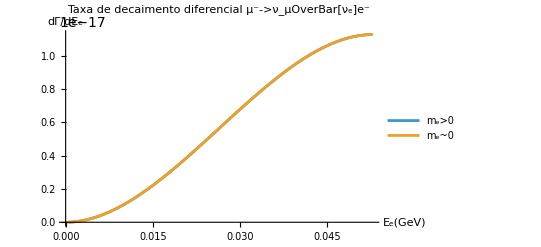

```mathematica
G=1.16*10^(-5) (*Gev^-2*)
me=0.51*10^(-3) (*GeV*)
mmu=105.65*10^(-3)(*GeV*)
Gam[x_]:= (G^2 /(12*Pi^3))*(3*me^2*x-2*me^2 *mmu-4*x^2*mmu+3*mmu^2*x)*Sqrt[x^2-me^2]
GamAprox[x_]:=(G^2/(12*Pi^3))*mmu^2*x^2(3 - (4*x/mmu))

Plot[{Gam[x],GamAprox[x]},{x,0,mmu/2},PlotLabel->"Taxa de decaimento diferencial μ^-->ν_μOverBar[ν_e]e^-", AxesLabel->{"E_e(GeV)","dΓ/dE_e"},PlotLegends->{"m_e>0","m_e~0"}]
```

```mathematica
G=1.16*10^(-5) (*Gev^-2*)
(*me=0.51*10^(-3)*) (*GeV*)
(*mmu=105.65*10^(-3)*)(*GeV*)
Gam[x_,me_,mmu_]:= (G^2 /(12*Pi^3))*(3*me^2*x-2*me^2 *mmu-4*x^2*mmu+3*mmu^2*x)*Sqrt[x^2-me^2]
GamAprox[x_,mmu_]:=(G^2/(12*Pi^3))*mmu^2*x^2(3 - (4*x/mmu))
Manipulate[Plot[{Gam[x,me,mmu],GamAprox[x,mmu]},{x,0,105.65*10^-3/2},PlotLabel->"Taxa de decaimento diferencial μ^-->ν_μOverBar[ν_e]e^-", AxesLabel->{"E_e(GeV)","dΓ/dE_e"},PlotLegends->{"m_e>0","m_e~0"}],{me,0,100*10^-3,1*10^-3},{mmu,0,105.65*10^-3,1*10^-3}]
Plot[{Gam[x,me],GamAprox[x]},{x,0,mmu/2},PlotLabel->"Taxa de decaimento diferencial μ^-->ν_μOverBar[ν_e]e^-", AxesLabel->{"E_e(GeV)","dΓ/dE_e"},PlotLegends->{"m_e>0","m_e~0"}]
```

0.0000116

-Graphics-

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.